alpha = 2, q0 = (1,0,0)

circular tip (kappa_c,s_c) = {0.620403,0.759836}

theta* = 3.05, kappa_theta = 0.0768558

tongue intersections: z_low = 0.87616, z_up = 1921.3

sample interior heights: Z_in = 0.506624, Z_out = 1980.19

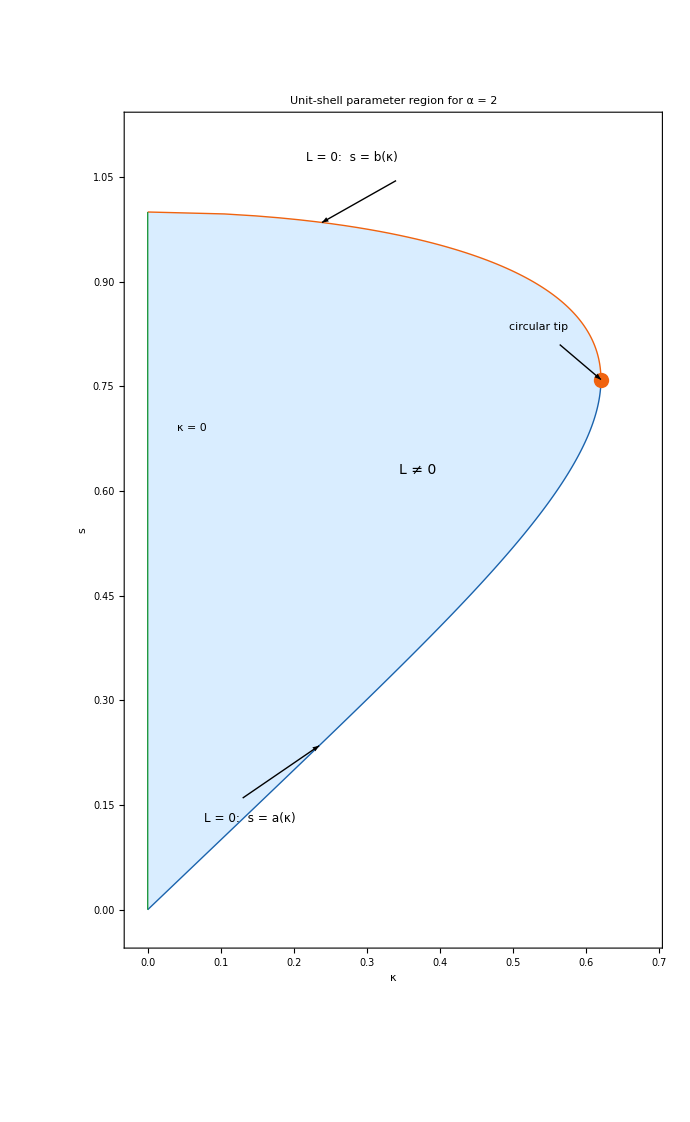

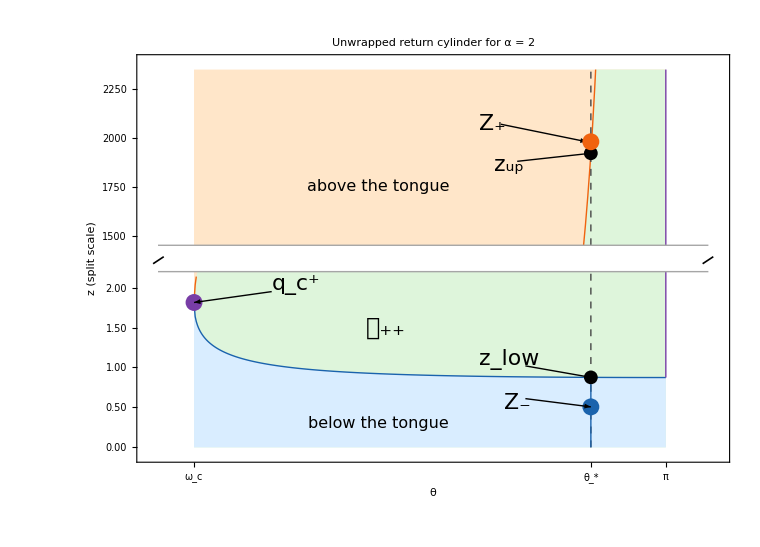

```mathematica
(* Reproducible Figures 3 and 4 for "Optimal Synthesis on a Radially Symmetric Grushin Space".
   Normalization: alpha = 2, q0 = (1,0,0), 2E = 1.
   Evaluate this file in Wolfram Language / Mathematica. It exports two vector PDFs and PNGs
   into ./figures relative to the current working directory. No external packages needed.

   Figure 3: unit-shell parameter region in (kappa,s).
   Figure 4: unwrapped cylinder (theta,z) with a broken height scale, the tongue,
             inward/outward first-return families at theta = thetaSample, and both
             intersections with the full-period boundary.
*)

ClearAll[alpha, sCrit, kappaCrit, omegaCrit, zCircular, kappaFromS,
  aOf, bOf, turningRadii, uPhi, denPhi, timeIntegral, angleIntegral,
  pFull, omegaFull, zLow, zUp, kappaAtAngle, phaseAtAngle,
  firstReturnHeight, firstReturnData, thetaSample, kappaTheta,
  kappaInSample, kappaOutSample, zInSample, zOutSample,
  zBoundaryLow, zBoundaryUp, pZero, zSpine, kappaGrid, tongueData,
  lowerPoints, upperPoints, upperPointsLow, upperPointsHigh,
  blue, orange, green, paleBlue, paleOrange, paleGreen, purple,
  figureParameter, figureReturns, outputDir,mathLabel];


mathLabel[expr_, size_: 20] :=
  Style[
    TraditionalForm[expr],
    FontSize -> size,
    Black
  ];
alpha = 2;
sCrit = N[(alpha + 1)^(-1/(2 alpha))];
kappaCrit = N[Sqrt[alpha] (alpha + 1)^(-(alpha + 1)/(2 alpha))];
omegaCrit = N[2 Pi/Sqrt[2 (alpha + 1)]];
zCircular = N[2 Pi/Sqrt[2 alpha (alpha + 1)]];
pZero = N[Beta[1/(2 alpha), 1/2]/alpha];
zSpine = pZero/(alpha + 1);

(* Q_kappa(s) >= 0 iff kappa <= s Sqrt[1-s^(2 alpha)], 0 < s <= 1.
   The upper and lower boundaries meet at (kappaCrit,sCrit). *)
kappaFromS[s_?NumericQ] := s Sqrt[Max[0., 1. - s^(2 alpha)]];

blue = RGBColor[0.10, 0.39, 0.68];
orange = RGBColor[0.94, 0.39, 0.06];
green = RGBColor[0.13, 0.60, 0.25];
paleBlue = RGBColor[0.85, 0.93, 1.00];
paleOrange = RGBColor[1.00, 0.90, 0.79];
paleGreen = RGBColor[0.87, 0.96, 0.86];
purple = RGBColor[0.47, 0.24, 0.65];

(* ===== FIGURE 3: parameter domain ===== *)
Module[{sValues, boundary, lower, upper},
  sValues = N[Subdivide[0, 1, 360]];
  boundary = ({kappaFromS[#], #} & /@ sValues);
  lower = Select[boundary, #[[2]] <= sCrit &];
  upper = Select[boundary, #[[2]] >= sCrit &];
  lower = Append[lower, {kappaCrit, sCrit}];
  upper = Prepend[upper, {kappaCrit, sCrit}];
  figureParameter = Graphics[
    {
      {paleBlue, EdgeForm[None], Polygon[Join[{{0., 0.}}, boundary, {{0., 1.}}]]},
      {Directive[blue, Thick], Line[lower]},
      {Directive[orange, Thick], Line[upper]},
      {Directive[green, Thick], Line[{{0, 0}, {0, 1}}]},
      {Directive[orange, PointSize[0.016]], Point[{kappaCrit, sCrit}]},
      {Directive[Black, Thin], Arrowheads[.025],Arrow[{{0.34, 1.045}, {kappaFromS[0.985], 0.985}}]},
      {Directive[Black, Thin], Arrowheads[.025],Arrow[{{0.13, 0.16}, {kappaFromS[0.235], 0.235}}]},
      Text[Style["L = 0:  s = b(κ)", 12], {0.28, 1.078}],
      Text[Style["L = 0:  s = a(κ)", 12], {0.14, 0.13}],
      Text[Style["L ≠ 0", 14], {0.37, 0.63}],
      Text[Style["κ = 0", 11], {0.06, 0.69}],
      Text[Style["circular tip", 11], {0.535, 0.835}],
      {Directive[Black, Thin],Arrowheads[.025], Arrow[{{0.564, 0.81}, {kappaCrit, sCrit}}]}
    },
    PlotRange -> {{-0.018, kappaCrit + 0.07}, {-0.032, 1.12}},
    PlotRangeClipping -> False,
    Frame -> True, Axes -> False,
    FrameLabel -> {Style["κ", 15], Style["s", 15]},
    PlotLabel -> Style["Unit-shell parameter region for α = 2", 14],
    BaseStyle -> {FontFamily -> "Times", FontSize -> 12},
    ImagePadding -> {{62, 25}, {50, 42}}, ImageSize -> 690
  ];
];

(* ===== NUMERICS FOR FIGURE 4 =====
   For alpha = 2 and Q(u) = 1-kappa^2/u^2-u^4, the turning radii a<b obey
       Q(u) = (u^2-a^2)(b^2-u^2)(u^2+a^2+b^2)/u^2.
   With u = a + (b-a) Sin[t]^2, the square-root endpoint singularities cancel.
   The following integrands are smooth on 0 <= t <= Pi/2 for 0 < kappa < kappaCrit.
   Bisection is used for the turning radii, angular inversion, and return phase.
*)

aOf[k_?NumericQ] := aOf[k] = Module[{lo = 0., hi = sCrit, mid},
  If[k <= 0, Return[0.]];
  If[k >= kappaCrit, Return[sCrit]];
  Do[mid = (lo + hi)/2.; If[kappaFromS[mid] < k, lo = mid, hi = mid], {62}];
  (lo + hi)/2.
];
bOf[k_?NumericQ] := bOf[k] = Module[{lo = sCrit, hi = 1., mid},
  If[k <= 0, Return[1.]];
  If[k >= kappaCrit, Return[sCrit]];
  Do[mid = (lo + hi)/2.; If[kappaFromS[mid] > k, lo = mid, hi = mid], {62}];
  (lo + hi)/2.
];
turningRadii[k_?NumericQ] := turningRadii[k] = {aOf[k], bOf[k]};

uPhi[k_?NumericQ, t_?NumericQ] := Module[{ab = turningRadii[k]},
  ab[[1]] + (ab[[2]] - ab[[1]]) Sin[t]^2
];
denPhi[k_?NumericQ, t_?NumericQ] := Module[{ab = turningRadii[k], u},
  u = uPhi[k, t];
  Sqrt[(u + ab[[1]]) (u + ab[[2]]) (u^2 + ab[[1]]^2 + ab[[2]]^2)]
];
(* timeIntegral = 2 Integral[du / Sqrt[Q]], angleIntegral = 2 kappa Integral[du/(u^2 Sqrt[Q])]. *)
timeIntegral[k_?NumericQ, t0_?NumericQ, t1_?NumericQ] := NIntegrate[
  4 uPhi[k, t]/denPhi[k, t], {t, t0, t1},
  AccuracyGoal -> 9, PrecisionGoal -> 9, MaxRecursion -> 12
];
angleIntegral[k_?NumericQ, t0_?NumericQ, t1_?NumericQ] := NIntegrate[
  4 k/(uPhi[k, t] denPhi[k, t]), {t, t0, t1},
  AccuracyGoal -> 9, PrecisionGoal -> 9, MaxRecursion -> 12
];

pFull[k_?NumericQ] := pFull[k] = Which[
  k <= 0, pZero,
  k >= kappaCrit, N[sCrit 2 Pi/Sqrt[2 alpha]],
  True, timeIntegral[k, 0., N[Pi/2]]
];
omegaFull[k_?NumericQ] := omegaFull[k] = Which[
  k <= 0, N[Pi],
  k >= kappaCrit, omegaCrit,
  True, angleIntegral[k, 0., N[Pi/2]]
];
zLow[k_?NumericQ] := Which[
  k <= 0, zSpine,
  k >= kappaCrit, zCircular,
  True, pFull[k]/((alpha + 1) bOf[k]^(alpha + 1))
];
zUp[k_?NumericQ] := Which[
  k <= 0, Infinity,
  k >= kappaCrit, zCircular,
  True, pFull[k]/((alpha + 1) aOf[k]^(alpha + 1))
];

(* Use an angle near Pi to make the high/low split legible, as in the manuscript. *)
thetaSample = 3.05;
kappaAtAngle[angle_?NumericQ] := Module[{lo = 0., hi = kappaCrit, mid},
  Do[mid = (lo + hi)/2.;
     If[omegaFull[mid] > angle, lo = mid, hi = mid], {43}];
  (lo + hi)/2.
];
kappaTheta = kappaAtAngle[thetaSample];
zBoundaryLow = zLow[kappaTheta];
zBoundaryUp = zUp[kappaTheta];

(* For fixed theta, the two premature-return families project to vertical height
   curves in the (theta,z) unwrapping. Their boundary intersections are reached
   as kappa increases to kappaTheta. We mark one genuine interior return on each. *)
phaseAtAngle[k_?NumericQ, target_?NumericQ] := Module[
  {lo = 0., hi = N[Pi/2], mid},
  Do[mid = (lo + hi)/2.;
     If[angleIntegral[k, 0., mid] < target, lo = mid, hi = mid], {38}];
  (lo + hi)/2.
];
firstReturnData[k_?NumericQ, branch_String] := Module[
  {phase, rad, radialL, tau, target, height},
  target = If[branch === "in", thetaSample, omegaFull[k] - thetaSample];
  phase = phaseAtAngle[k, target];
  rad = uPhi[k, phase];
  radialL = Sqrt[Max[0., 1 - k^2/rad^2 - rad^(2 alpha)]];
  tau = If[branch === "in",
    timeIntegral[k, 0., phase]/rad,
    timeIntegral[k, phase, N[Pi/2]]/rad
  ];
  height = (tau + If[branch === "in", -2 radialL, 2 radialL])/
    ((alpha + 1) rad^alpha);
  {height, rad, tau}
];
firstReturnHeight[k_?NumericQ, branch_String] := firstReturnData[k, branch][[1]];
kappaInSample = 0.70 kappaTheta;
kappaOutSample = 0.99 kappaTheta;
zInSample = firstReturnHeight[kappaInSample, "in"];
zOutSample = firstReturnHeight[kappaOutSample, "out"];

Print["alpha = ", alpha, ", q0 = (1,0,0)"];
Print["circular tip (kappa_c,s_c) = ", N[{kappaCrit, sCrit}, 8]];
Print["theta* = ", thetaSample, ", kappa_theta = ", N[kappaTheta, 8]];
Print["tongue intersections: z_low = ", N[zBoundaryLow, 8],
      ", z_up = ", N[zBoundaryUp, 8]];
Print["sample interior heights: Z_in = ", N[zInSample, 8],
      ", Z_out = ", N[zOutSample, 8]];
If[!(0 < zInSample < zBoundaryLow < zBoundaryUp < zOutSample),
  Print["WARNING: first-return separation check failed."]
];

(* Sample the full-period boundary in kappa, ordering the results by increasing theta.
   The kappa=0 upper endpoint is at +Infinity and is represented by the spine,
   not passed to Graphics as a finite point. *)
kappaGrid = N[Subdivide[kappaCrit (1 - 10^-5), 0.02, 250]];
tongueData = Join[
  {{omegaCrit, zCircular, zCircular}},
  Table[{omegaFull[k], zLow[k], zUp[k]}, {k, kappaGrid}]
];
lowerPoints = Append[({#[[1]], #[[2]]} & /@ tongueData), {N[Pi], zSpine}];
upperPoints = ({#[[1]], #[[3]]} & /@ tongueData);

(* Figure 4 is drawn as ONE Graphics object with two explicit height windows.
   This avoids front-end dependent sizing/clipping in GraphicsColumn.  The height
   transformation changes only the DISPLAY coordinate; all numerical z values
   and all endpoint formulas above are unchanged. *)
   (* Cut locus *)
labelTongue =
  mathLabel[Subscript[𝒞, "++"], 24];

(* Boundary curves *)
labelLow =
  mathLabel[Subscript["z", "low"], 22];

labelUp =
  mathLabel[Subscript["z", "up"], 22];

(* Premature return heights *)
labelMinus =
  mathLabel[Subscript["Z", "-"], 22];

labelPlus =
  mathLabel[Subscript["Z", "+"], 22];

(* Distinguished points *)
labelCircular =
  mathLabel[Subsuperscript["q", "c", "+"], 22];

labelSpine =
  mathLabel[𝒮, 22];

(* Angular coordinates *)
labelTheta =
  mathLabel[Subscript[θ, "*"], 20];

labelOmega =
  mathLabel[Subscript[ω, "c"], 20];
Module[{xLeft, xRight, zLowMin, zLowMax, zHighMin, zHighMax,
        lowY, highY, lowerXY, upperLowXY, upperHighXY, upperCrossingAngle,
        lowFill, lowTongue, lowAbove, highTongue, lowTicks, highTicks,
        xTicks, yBottom, yLowTop, yHighBottom, yTop},
  xLeft = omegaCrit - 0.044;
  xRight = N[Pi] + 0.052;
  zLowMin = 0.; zLowMax = 2.20;
  zHighMin = 1450.; zHighMax = 2350.;
  yBottom = 0.; yLowTop = 1.; yHighBottom = 1.15; yTop = 2.15;
  lowY[z_?NumericQ] := yBottom + (z-zLowMin)/(zLowMax-zLowMin) (yLowTop-yBottom);
  highY[z_?NumericQ] := yHighBottom + (z-zHighMin)/(zHighMax-zHighMin) (yTop-yHighBottom);

  lowerXY = ({#[[1]], lowY[#[[2]]]} & /@ lowerPoints);
  upperLowXY = Append[
    ({#[[1]], lowY[Clip[#[[2]], {zLowMin,zLowMax}]]} & /@ upperPoints),
    {N[Pi], yLowTop}
  ];
  (* Interpolate the actual upper boundary at both ends of the upper window.
     This avoids truncating the curve at the first/last sampled point, and
     does not introduce an artificial vertical boundary at thetaSample. *)
  upperCrossingAngle[z_?NumericQ] := Module[{pair},
    pair = First[Select[Partition[upperPoints, 2, 1],
      #[[1, 2]] <= z <= #[[2, 2]] &]];
    pair[[1, 1]] + (z - pair[[1, 2]])
      (pair[[2, 1]] - pair[[1, 1]])/(pair[[2, 2]] - pair[[1, 2]])
  ];
  upperHighXY = Join[
    {{upperCrossingAngle[zHighMin], yHighBottom}},
    ({#[[1]], highY[#[[2]]]} & /@
      Select[upperPoints, zHighMin < #[[2]] < zHighMax &]),
    {{upperCrossingAngle[zHighMax], yTop}}
  ];
  lowFill = Polygon[Join[{{omegaCrit, yBottom}}, lowerXY, {{N[Pi], yBottom}}]];
  lowAbove = Polygon[Join[upperLowXY, {{omegaCrit, yLowTop}}]];
  highTongue = Polygon[Join[upperHighXY,
    {{N[Pi], yTop}, {N[Pi], yHighBottom}}]];

  lowTicks = ({lowY[#], NumberForm[#, {3, 2}]} & /@ {0., 0.5, 1., 1.5, 2.});
  highTicks = ({highY[#], ToString[Round[#]]} & /@ {1500., 1750., 2000., 2250.});
 xTicks = {
  {omegaCrit, labelOmega},
  {thetaSample, labelTheta},
  {N[Pi], mathLabel[π, 20]}
};

  figureReturns = Graphics[
    {
      (* LOWER WINDOW: zero <= z <= 2.20. *)
      {paleGreen, EdgeForm[None], Rectangle[{omegaCrit, yBottom}, {N[Pi], yLowTop}]},
      {paleBlue, EdgeForm[None], lowFill},
      {paleOrange, EdgeForm[None], lowAbove},
      {Directive[blue, Thick], Line[lowerXY]},
      {Directive[orange, Thick],
       Line[Select[upperLowXY, #[[2]] < yLowTop - 10^-7 &]]},
      {Directive[purple, Thick], Line[{{N[Pi], lowY[zSpine]}, {N[Pi], yLowTop}}]},
      {Directive[GrayLevel[0.27], Dashed],
       Line[{{thetaSample, yBottom}, {thetaSample, yLowTop}}]},
      {Directive[blue, Thick],
       Line[{{thetaSample, yBottom}, {thetaSample, lowY[zBoundaryLow]}}]},
      {Directive[Black, PointSize[0.013]], Point[{thetaSample, lowY[zBoundaryLow]}]},
      {Directive[blue, PointSize[0.016]], Point[{thetaSample, lowY[zInSample]}]},
      {Directive[purple, PointSize[0.016]], Point[{omegaCrit, lowY[zCircular]}]},
      Inset[labelCircular,{2.69,.03+lowY[1.97]}],
      {Directive[Black, Thin],Arrowheads[.025],
       Arrow[{{2.66, lowY[1.95]}, {omegaCrit, lowY[zCircular]}}]},
       Inset[labelTongue, {2.80, lowY[1.50]}],
      Text[Style["below the tongue", 16], {2.79, lowY[0.30]}],
      Inset[labelMinus, {2.96, 0.25}],
      {Directive[Black, Thin],Arrowheads[.025],
       Arrow[{{2.97, lowY[0.61]}, {thetaSample, lowY[zInSample]}}]},
      Inset[labelLow, {2.95, 0.5}],
      {Directive[Black, Thin],Arrowheads[.025],
       Arrow[{{2.97, lowY[1.02]}, {thetaSample, lowY[zBoundaryLow]}}]},

      (* UPPER WINDOW: 1450 <= z <= 2350. *)
      {paleOrange, EdgeForm[None],
       Rectangle[{omegaCrit, yHighBottom}, {N[Pi], yTop}]},
      {paleGreen, EdgeForm[None], highTongue},
      {Directive[orange, Thick], Line[upperHighXY]},
      {Directive[purple, Thick], Line[{{N[Pi], yHighBottom}, {N[Pi], yTop}}]},
      {Directive[GrayLevel[0.27], Dashed],
       Line[{{thetaSample, yHighBottom}, {thetaSample, yTop}}]},
      {Directive[Black, PointSize[0.013]], Point[{thetaSample, highY[zBoundaryUp]}]},
      {Directive[orange, PointSize[0.016]], Point[{thetaSample, highY[zOutSample]}]},
      Text[Style["above the tongue", 16], {2.79, highY[1750]}],
      Inset[labelPlus,{2.93,.1+highY[zOutSample]}],
      {Arrowheads[.025],Directive[Black, Thin],
       Arrow[{{2.94, highY[2070]}, {thetaSample-.005, highY[zOutSample]}}]},
       Inset[labelUp, {2.95, highY[1860]}],
      {Directive[Black, Thin],Arrowheads[.025],
       Arrow[{{2.96, highY[1880]}, {thetaSample, highY[zBoundaryUp]}}]},

      (* Thin panel borders and two slash marks make the omitted scale explicit. *)
      {Directive[GrayLevel[0.65], Thin],
       Line[{{xLeft, yLowTop}, {xRight, yLowTop}}],
       Line[{{xLeft, yHighBottom}, {xRight, yHighBottom}}]},
      {Directive[Black, AbsoluteThickness[1.2]],
       Line[{{xLeft - 0.006, 1.045}, {xLeft + 0.007, 1.085}}],
       Line[{{xRight - 0.007, 1.045}, {xRight + 0.006, 1.085}}]}
    },
    PlotRange -> {{xLeft - 0.012, xRight + 0.012}, {-0.04, yTop + 0.04}},
    PlotRangeClipping -> False, PlotRangePadding -> None,
    Frame -> True, Axes -> False,
    FrameTicks -> {{Join[lowTicks, highTicks], None}, {xTicks, None}},
    FrameLabel -> {Style["θ", 20], Style["z (split scale)", 20]},
    PlotLabel -> Style["Unwrapped return cylinder for α = 2", 14],
    BaseStyle -> {FontFamily -> "Times", FontSize -> 11},
    ImagePadding -> {{72, 25}, {48, 40}}, ImageSize -> {760, 575},
    AspectRatio -> 0.72
  ];
];

(* Exports are vector PDFs plus quick-look PNGs. These are the only output files. *)
(*outputDir = FileNameJoin[{Directory[], "figures"}];
If[!DirectoryQ[outputDir], CreateDirectory[outputDir, CreateIntermediateDirectories -> True]];
Export[FileNameJoin[{outputDir, "figure_A_parameter_region.pdf"}], figureParameter, "PDF"];
Export[FileNameJoin[{outputDir, "figure_A_parameter_region.png"}], figureParameter, "PNG", ImageResolution -> 220];
Export[FileNameJoin[{outputDir, "figure_B_unwrapped_tongue.pdf"}], figureReturns, "PDF"];
Export[FileNameJoin[{outputDir, "figure_B_unwrapped_tongue.png"}], figureReturns, "PNG", ImageResolution -> 220];
Print["Exported both figures to: ", outputDir];*)
figureParameter
figureReturns
```

```mathematica
(* ================================================================*)(*Premature conjugacy for f(r)=r Exp[-1/r^2]*)(*q0=(1,0,0),H=1/2*)(* ================================================================*)

wp=50;

(*Exact parameter choices,converted only afterwards to high precision*)
K0=N[9/10,wp];
qpar=N[4/5,wp];

L0=N[Sqrt[(1-(9/10)^2) (1-(4/5)^2)],wp];

W0=N[(4/5) Exp[1] Sqrt[1-(9/10)^2],wp];

Print["Initial covector (L,K,w) = ",N[{L0,K0,W0},16]];


(* ================================================================*)(*1. Radial period*)(* ================================================================*)wp=50;
guard=30;
wpRoot=wp+guard;

(*Keep the defining parameters exact as long as possible*)
Kexact=9/10;
qexact=4/5;
Wexact=qexact E Sqrt[1-Kexact^2];

radExact[r_]:=1-Kexact^2/r^2-Wexact^2 r^2 Exp[-2/r^2];

(*Turning points computed with guard digits*)
rminus=r/. FindRoot[radExact[r]==0,{r,N[47/50,wpRoot]},WorkingPrecision->wpRoot,AccuracyGoal->60,PrecisionGoal->60];

rplus=r/. FindRoot[radExact[r]==0,{r,N[34/25,wpRoot]},WorkingPrecision->wpRoot,AccuracyGoal->60,PrecisionGoal->60];

mid=(rminus+rplus)/2;
half=(rplus-rminus)/2;

P=2 NIntegrate[half Cos[phi]/Sqrt[radExact[mid+half Sin[phi]]],{phi,-Pi/2,Pi/2},WorkingPrecision->wp,AccuracyGoal->30,PrecisionGoal->30,MaxRecursion->30,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];

Print["r_- = ",N[rminus,16]];
Print["r_+ = ",N[rplus,16]];
Print["Radial period P = ",N[P,16]];


(* ================================================================*)
(*2. Hamiltonian equations*)
(* ================================================================*)

stateEq={x'[t]==u[t],y'[t]==v[t],z'[t]==ww[t] (x[t]^2+y[t]^2) Exp[-2/(x[t]^2+y[t]^2)],u'[t]==-ww[t]^2 x[t] Exp[-2/(x[t]^2+y[t]^2)] (1+2/(x[t]^2+y[t]^2)),v'[t]==-ww[t]^2 y[t] Exp[-2/(x[t]^2+y[t]^2)] (1+2/(x[t]^2+y[t]^2)),ww'[t]==0};

stateIC={x[0]==1,y[0]==0,z[0]==0,u[0]==L0,v[0]==K0,ww[0]==W0};


(* ================================================================*)
(*3. Linearized Hamiltonian system*)
(* ================================================================*)

jac[xv_,yv_,zv_,uv_,vv_,wv_]:=Module[{r2,ef,g,a,ax,ay},r2=xv^2+yv^2;
ef=Exp[-2/r2];
g=r2 ef;
a=ef (1+2/r2);
(*derivatives of a with respect to x and y*)ax=8 ef xv/r2^3;
ay=8 ef yv/r2^3;
{{0,0,0,1,0,0},{0,0,0,0,1,0},{2 wv a xv,2 wv a yv,0,0,0,g},{-wv^2 (a+xv ax),-wv^2 xv ay,0,0,0,-2 wv a xv},{-wv^2 yv ax,-wv^2 (a+yv ay),0,0,0,-2 wv a yv},{0,0,0,0,0,0}}];


(*Create 18 scalar sensitivity variables s11,...,s63*)
sNames=Table[Symbol["s"<>ToString[i]<>ToString[j]],{i,6},{j,3}];

sMat[t_]:=Map[#[t]&,sNames,{2}];

Jmat[t_]:=jac[x[t],y[t],z[t],u[t],v[t],ww[t]];

sensEq=Thread[Flatten[D[sMat[t],t]]==Flatten[Jmat[t].sMat[t]]];

(*derivative with respect to initial (L,K,w)=(u0,v0,w0)*)
S0=Join[ConstantArray[0,{3,3}],IdentityMatrix[3]];

sensIC=Thread[Flatten[sMat[0]]==Flatten[S0]];


(* ================================================================*)
(*4. Solve state+variational equations*)
(* ================================================================*)

depVars=Join[{x,y,z,u,v,ww},Flatten[sNames]];

tmax=N[93/25,wp];

sol=NDSolveValue[Join[stateEq,stateIC,sensEq,sensIC],depVars,{t,0,tmax},WorkingPrecision->wp,AccuracyGoal->30,PrecisionGoal->30,MaxStepSize->N[1/2000,wp],MaxSteps->Infinity];


(*The first six entries are the Hamiltonian variables.Entries 7,...,24 are the sensitivity matrix.*)

sSol=Partition[sol[[7;;24]],3];

Snum[tt_?NumericQ]:=Map[#[tt]&,sSol,{2}];

(*endpoint differential d(x,y,z)/d(L,K,w)*)
endpointJac[tt_?NumericQ]:=Snum[tt][[1;;3,All]];

detEnd[tt_?NumericQ]:=Det[endpointJac[tt]];


(* ================================================================*)
(*5. Locate the first transverse zero*)
(* ================================================================*)

grid=N[Subdivide[1/100,P-1/10000,6000],wp];

vals=detEnd/@grid;

crossings=Select[Partition[Transpose[{grid,vals}],2,1],#[[1,2]] #[[2,2]]<0&];

If[crossings==={},Print["No sign-changing zero found."];
Abort[];];

bracket=First[crossings][[All,1]];

tcon=t/. FindRoot[detEnd[t]==0,{t,bracket[[1]],bracket[[2]]},WorkingPrecision->wp,AccuracyGoal->25,PrecisionGoal->25];


(* ================================================================*)
(*6. Output*)
(* ================================================================*)

Print["First conjugate time = ",N[tcon,16]];
Print["t_con/P = ",N[tcon/P,16]];
Print["P - t_con = ",N[P-tcon,16]];

Print["det J(t_con - .001) = ",N[detEnd[tcon-1/1000],14]];

Print["det J(t_con + .001) = ",N[detEnd[tcon+1/1000],14]];

Print["Singular values at t_con = ",N[SingularValueList[endpointJac[tcon]],14]];
```

Initial covector (L,K,w) = {0.2615339366124404,0.9,0.9478972632252754}

r_- = 0.9394663574245576

r_+ = 1.358554112929916

Radial period P = 3.702642000500497

First conjugate time = 3.695907275106391

t_con/P = 0.9981811027387483

P - t_con = 0.00673472539410574

det J(t_con - .001) = 0.0089726760392528

det J(t_con + .001) = -0.0089738201125466

Singular values at t_con = {3.4913610494181,2.5400713494846}

```mathematica
(*Code to Make the simulation of geodesics figure*)
```

```mathematica
tol=10^-10;

MakePair[K_,w_]:=Module[{L2=1-K^2-w^2},If[L2<=0,Return[$Failed]];
{{Sqrt[L2],K,w},{-Sqrt[L2],K,w}}];

PiAlpha[alpha_]:=Beta[1/(2 alpha),1/2]/alpha;
```

```mathematica
ClearAll[TurningRadii];

TurningRadii[alpha_?NumericQ,{L_,K_,w_}]:=Module[{kk=Abs[N[K]],ww=Abs[N[w]],rc,q,hi,rm,rp},If[ww<tol,Return[{0.,Infinity}]];
If[kk<tol,Return[{0.,ww^(-1/alpha)}]];
q[r_?NumericQ]:=1-kk^2/r^2-ww^2 r^(2 alpha);
rc=(kk^2/(alpha ww^2))^(1/(2 alpha+2));
(*Circular orbit*)If[Abs[q[rc]]<10^-9,Return[{rc,rc}]];
hi=Max[2 rc,2 ww^(-1/alpha),2.];
While[q[hi]>0,hi*=2];
rm=r/. FindRoot[q[r]==0,{r,rc 10^-6,rc},Method->"Brent"];
rp=r/. FindRoot[q[r]==0,{r,rc,hi},Method->"Brent"];
{rm,rp}];
```

```mathematica
ClearAll[PAlpha];

PAlpha[alpha_?NumericQ,cov:{L_,K_,w_}]:=Module[{kk=Abs[N[K]],ww=Abs[N[w]],rm,rp,d,q,qp,g},If[ww<tol,Return[Infinity]];
If[kk<tol,Return[N[PiAlpha[alpha] ww^(-1/alpha)]]];
{rm,rp}=TurningRadii[alpha,cov];
(*Circular limiting radial period*)If[Abs[rp-rm]<10^-8,Return[N[2 Pi/Sqrt[2 alpha]]]];
d=rp-rm;
q[r_?NumericQ]:=1-kk^2/r^2-ww^2 r^(2 alpha);
qp[r_?NumericQ]:=2 kk^2/r^3-2 alpha ww^2 r^(2 alpha-1);
g[u_?NumericQ]:=Which[Abs[u]<10^-8,2 Sqrt[d/qp[rm]],Abs[u-Pi/2]<10^-8,2 Sqrt[d/(-qp[rp])],True,With[{r=rm+d Sin[u]^2},2 d Sin[u] Cos[u]/Sqrt[Max[q[r],0.]]]];
2 NIntegrate[g[u],{u,0,Pi/2},Method->"LocalAdaptive",AccuracyGoal->10,PrecisionGoal->10]];
```

```mathematica
ClearAll[GeodesicSolution];

GeodesicSolution[alpha_?NumericQ,cov:{L_,K_,w_}]:=Module[{ll=N[L],kk=N[K],ww=N[w],P,sol},P=PAlpha[alpha,cov];
If[Abs[kk]<tol,sol=NDSolveValue[{x'[t]==px[t],px'[t]==-alpha ww^2 Abs[x[t]]^(2 alpha-2) x[t],z'[t]==ww Abs[x[t]]^(2 alpha),x[0]==1,px[0]==ll,z[0]==0},{x,px,z},{t,0,P},MaxSteps->Infinity];
<|"Period"->P,"Position"->Function[{tt},{sol[[1]][tt],0,sol[[3]][tt]}]|>,sol=NDSolveValue[{r'[t]==pr[t],pr'[t]==kk^2/r[t]^3-alpha ww^2 r[t]^(2 alpha-1),th'[t]==kk/r[t]^2,z'[t]==ww r[t]^(2 alpha),r[0]==1,pr[0]==ll,th[0]==0,z[0]==0},{r,pr,th,z},{t,0,P},MaxSteps->Infinity];
<|"Period"->P,"Position"->Function[{tt},{sol[[1]][tt] Cos[sol[[3]][tt]],sol[[1]][tt] Sin[sol[[3]][tt]],sol[[4]][tt]}]|>]]
```

```mathematica
ClearAll[GeodesicPlot];

GeodesicPlot[alpha_?NumericQ,cov_,style_:Directive[Blue,Thick]]:=Module[{g,P,pos},g=GeodesicSolution[alpha,cov];
P=g["Period"];
pos=g["Position"];
ParametricPlot3D[Evaluate[pos[t]],{t,0,P},PlotStyle->style,PlotPoints->150,MaxRecursion->3,AxesLabel->{"x","y","z"},PlotRange->All]];
```

```mathematica
alpha0=2;

families={<|"Label"->"generic 1","Covectors"->MakePair[1/4,2/5]|>,<|"Label"->"generic 2","Covectors"->MakePair[1/2,1/3]|>,<|"Label"->"generic 3","Covectors"->MakePair[1/3,2/3]|>,<|"Label"->"K = 0, family 1","Covectors"->MakePair[0,1/2]|>,<|"Label"->"K = 0, family 2","Covectors"->MakePair[0,3/4]|>,(*Noncircular L=0 example*)<|"Label"->"L = 0","Covectors"->{{0,4/5,3/5}}|>};
```

```mathematica
colors=Table[ColorData[97][j],{j,Length[families]}];

ClearAll[FamilyPlot];

FamilyPlot[alpha_,covectors_,color_]:=Module[{data,curves,endpoint},data=GeodesicSolution[alpha,#]&/@covectors;
curves=MapIndexed[Function[{g,j},Module[{style,pos,P},style=If[First[j]==1,Directive[color,Thick],Directive[color,Thick,Dashed]];
pos=g["Position"];
P=g["Period"];
ParametricPlot3D[Evaluate[pos[t]],{t,0,P},PlotStyle->style,PlotPoints->150,MaxRecursion->3,PlotRange->All]]],data];
endpoint=With[{g=First[data]},g["Position"][g["Period"]]];
Show[curves,Graphics3D[{color,PointSize[0.014],Point[endpoint]}]]];
```

```mathematica
(* ============================================================*)(*FINAL CUT-LOCUS FIGURE*)(*Assumes everything through FamilyPlot has already been run.*)(* ============================================================*)ClearAll[ScaledTurningRadii,ScaledOrbitData,aFun,bFun,pFun,omegaFun,zLow,zUp,zTop,TonguePatch,BoundaryCurve,CleanGeodesicPlot];

alphaFig=2;

kappaC[alpha_]:=Sqrt[alpha] (alpha+1)^(-(alpha+1)/(2 alpha));

sC[alpha_]:=(alpha+1)^(-1/(2 alpha));

omegaC[alpha_]:=2 Pi/Sqrt[2 (alpha+1)];

zCircular[alpha_]:=2 Pi/Sqrt[2 alpha (alpha+1)];

kc=N[kappaC[alphaFig]];
sc=N[sC[alphaFig]];


(*------------------------------------------------------------*)
(*Scaled turning radii for*)
(*Q_kappa(s)=1-kappa^2/s^2-s^(2 alpha).*)
(*------------------------------------------------------------*)

ScaledTurningRadii[alpha_?NumericQ,kap_?NumericQ]:=Module[{k=N[kap],kcrit,scrit,q,rc,aa,bb},kcrit=N[kappaC[alpha]];
scrit=N[sC[alpha]];
If[k<=10^-12,Return[{0.,1.}]];
If[Abs[k-kcrit]<=10^-10,Return[{scrit,scrit}]];
q[s_?NumericQ]:=1-k^2/s^2-s^(2 alpha);
rc=(k^2/alpha)^(1/(2 alpha+2));
aa=s/. FindRoot[q[s]==0,{s,k,rc},Method->"Brent"];
bb=s/. FindRoot[q[s]==0,{s,rc,1.},Method->"Brent"];
{aa,bb}];


(*------------------------------------------------------------*)
(*Scaled period p_alpha(kappa) and apsidal angle omega_alpha.*)
(*Endpoint singularities are removed by s=a+(b-a) Sin[u]^2.*)
(*------------------------------------------------------------*)

ClearAll[ScaledOrbitData];

ScaledOrbitData[alpha_?NumericQ,kap_?NumericQ]:=Module[{k=N[kap],kcrit,scrit,aa,bb,s,q,L,K,w,cov,g,P,endpoint,om},kcrit=N[kappaC[alpha]];
scrit=N[sC[alpha]];
(*K=0 limit*)If[k<=10^-10,Return[<|"a"->0.,"b"->1.,"p"->N[PiAlpha[alpha]],"omega"->N[Pi]|>]];
(*circular limit*)If[Abs[k-kcrit]<=10^-8,Return[<|"a"->scrit,"b"->scrit,"p"->N[2 Pi scrit/Sqrt[2 alpha]],"omega"->N[omegaC[alpha]]|>]];
{aa,bb}=ScaledTurningRadii[alpha,k];
(*Choose any interior scaled initial radius.*)s=(aa+bb)/2;
q=1-k^2/s^2-s^(2 alpha);
w=s^alpha;
K=k/s;
L=Sqrt[Max[q,0.]];
cov={L,K,w};
(*Existing,already-tested machinery*)g=GeodesicSolution[alpha,cov];
P=g["Period"];
(*Since s=w^(1/alpha),p_alpha=s P_alpha.*)endpoint=g["Position"][P];
om=ArcTan[endpoint[[1]],endpoint[[2]]];
<|"a"->aa,"b"->bb,"p"->N[s P],"omega"->N[om]|>]


(*------------------------------------------------------------*)
(*Precompute and interpolate.*)
(*This makes the actual 3D plotting fast and smooth.*)
(*------------------------------------------------------------*)

nGrid=100;
epsK=10^-4;


kappaGrid=Join[{0.},Subdivide[epsK kc,(1-epsK) kc,nGrid-2],{kc}];
orbitTable=ScaledOrbitData[alphaFig,#]&/@kappaGrid;

aFun=Interpolation[Transpose[{kappaGrid,Lookup[orbitTable,"a"]}],InterpolationOrder->3];

bFun=Interpolation[Transpose[{kappaGrid,Lookup[orbitTable,"b"]}],InterpolationOrder->3];

pFun=Interpolation[Transpose[{kappaGrid,Lookup[orbitTable,"p"]}],InterpolationOrder->3];

omegaFun=Interpolation[Transpose[{kappaGrid,Lookup[orbitTable,"omega"]}],InterpolationOrder->3];


(*------------------------------------------------------------*)
(*Cut-locus height functions.*)
(*s=b gives lower boundary;s=a gives upper boundary.*)
(*------------------------------------------------------------*)

zLow[k_?NumericQ]:=pFun[k]/((alphaFig+1) bFun[k]^(alphaFig+1));

zUp[k_?NumericQ]:=pFun[k]/((alphaFig+1) aFun[k]^(alphaFig+1));


(*Crop the infinite antipodal spine for the figure only.*)
zMax=3.25;

zTop[k_?NumericQ]:=If[k<10^-8,zMax,Min[zUp[k],zMax]];


(*------------------------------------------------------------*)
(*Smooth cut-locus surfaces.*)
(*signK reflects across the antipodal meridian.*)
(*signZ reflects across z=0.*)
(*------------------------------------------------------------*)

cutStyle=Directive[RGBColor[0.32,0.60,0.82],Opacity[0.52]];

boundaryStyle=Directive[GrayLevel[0.12],AbsoluteThickness[1.7]];


TonguePatch[signK_Integer,signZ_Integer]:=ParametricPlot3D[Evaluate[{Cos[signK omegaFun[k]],Sin[signK omegaFun[k]],signZ ((1-u) zLow[k]+u zTop[k])}],{k,0,kc},{u,0,1},Mesh->None,BoundaryStyle->None,PlotStyle->cutStyle,PlotPoints->{75,14},MaxRecursion->1,PlotRange->{{-1.15,1.15},{-1.15,1.15},{-zMax,zMax}}];


(*------------------------------------------------------------*)
(*Smooth true boundary curves.*)
(*We truncate the unbounded upper branch at z=zMax.*)
(*------------------------------------------------------------*)

boundaryInset=0.999;

kUpperStart=k/. FindRoot[zUp[k]==boundaryInset zMax,{k,10^-5 kc,kc},Method->"Brent"];


BoundaryCurve["low",signK_Integer,signZ_Integer]:=ParametricPlot3D[Evaluate[{Cos[signK omegaFun[k]],Sin[signK omegaFun[k]],signZ zLow[k]}],{k,0,kc},PlotStyle->boundaryStyle,PlotPoints->150,MaxRecursion->2];


BoundaryCurve["up",signK_Integer,signZ_Integer]:=ParametricPlot3D[Evaluate[{Cos[signK omegaFun[k]],Sin[signK omegaFun[k]],signZ zUp[k]}],{k,kUpperStart,kc},PlotStyle->boundaryStyle,PlotPoints->150,MaxRecursion->2];


(*------------------------------------------------------------*)
(*Antipodal spine K=0.*)
(*------------------------------------------------------------*)

zSpine=N[PiAlpha[alphaFig]/(alphaFig+1)];

spinePlot=Graphics3D[{Red,Dashed,Thickness[.00155],Line[{{-1,0,zSpine},{-1,0,zMax}}],Line[{{-1,0,-zSpine},{-1,0,-zMax}}]}];


(*------------------------------------------------------------*)
(*Faint reference cylinder r=1.*)
(*------------------------------------------------------------*)

cylinderPlot=ParametricPlot3D[{Cos[phi],Sin[phi],zz},{phi,0,2 Pi},{zz,-zMax,zMax},Mesh->None,BoundaryStyle->None,PlotStyle->Directive[GrayLevel[0.7],Opacity[0.055]],PlotPoints->{80,10}];


(*------------------------------------------------------------*)
(*Clean geodesic plotting:no endpoint dots.*)
(*------------------------------------------------------------*)

CleanGeodesicPlot[cov_,style_]:=Module[{g,per,pos},g=GeodesicSolution[alphaFig,cov];
per=g["Period"];
pos=g["Position"];
ParametricPlot3D[Evaluate[pos[t]],{t,0,per},PlotStyle->style,PlotPoints->180,MaxRecursion->3,PlotRange->All]];


(* ============================================================*)
(*THREE GEOMETRIC MECHANISMS*)
(* ============================================================*)


(*------------------------------------------------------------*)
(*1. Generic Maxwell pair:L<->-L.*)
(*Choose an interior point of the tongue.*)
(*------------------------------------------------------------*)

kGeneric=0.60 kc;

sGeneric=(aFun[kGeneric]+bFun[kGeneric])/2;

KGeneric=kGeneric/sGeneric;
wGeneric=sGeneric^alphaFig;

genericPair=MakePair[KGeneric,wGeneric];

genericPlot=Show[CleanGeodesicPlot[genericPair[[1]],Directive[RGBColor[0.78,0.18,0.16],AbsoluteThickness[3]]],CleanGeodesicPlot[genericPair[[2]],Directive[RGBColor[0.78,0.18,0.16],AbsoluteThickness[3],Dashed]]];
kGeneric2=0.55 kc;

sGeneric2=(aFun[kGeneric2]+bFun[kGeneric2])/2;

KGeneric2=-kGeneric2/sGeneric2;
wGeneric2=sGeneric2^alphaFig;

genericPair2=MakePair[KGeneric2,wGeneric2];

genericPlot2=Show[CleanGeodesicPlot[genericPair2[[1]],Directive[RGBColor[0.72,0.52,0.08],AbsoluteThickness[3]]],CleanGeodesicPlot[genericPair2[[2]],Directive[RGBColor[0.72,0.52,0.08],AbsoluteThickness[3],Dashed]]];

(*------------------------------------------------------------*)
(*2. K=0 pair:endpoint lies on the antipodal spine.*)
(*------------------------------------------------------------*)

wSpine=0.60;

spinePair=MakePair[0,wSpine];

spineGeodesics=Show[CleanGeodesicPlot[spinePair[[1]],Directive[RGBColor[0.14,0.48,0.20],AbsoluteThickness[2.1]]],CleanGeodesicPlot[spinePair[[2]],Directive[RGBColor[0.14,0.48,0.20],AbsoluteThickness[2.8],Dashed]]];


(*------------------------------------------------------------*)
(*3. L=0 boundary geodesic.*)
(*Choose the LOWER conjugate boundary,s=b(kappa).*)
(*------------------------------------------------------------*)

kBoundary=0.72 kc;
sBoundary=bFun[kBoundary];

KBoundary=kBoundary/sBoundary;
wBoundary=sBoundary^alphaFig;

boundaryCovector={0,KBoundary,wBoundary};

boundaryGeodesic=CleanGeodesicPlot[boundaryCovector,Directive[RGBColor[0.48,0.16,0.62],AbsoluteThickness[3]]];


(*------------------------------------------------------------*)
(*Base point q0=(1,0,0).*)
(*One small marker is useful here;there are no cut-locus dots.*)
(*------------------------------------------------------------*)

basePoint=Graphics3D[{Black,Sphere[{1,0,0},0.035]}];


(* ============================================================*)
(*CUT LOCUS*)
(* ============================================================*)

cutLocusPlot=Show[TonguePatch[1,1],TonguePatch[-1,1],TonguePatch[1,-1],TonguePatch[-1,-1],BoundaryCurve["low",1,1],BoundaryCurve["up",1,1],BoundaryCurve["low",-1,1],BoundaryCurve["up",-1,1],BoundaryCurve["low",1,-1],BoundaryCurve["up",1,-1],BoundaryCurve["low",-1,-1],BoundaryCurve["up",-1,-1],spinePlot];


(* ============================================================*)
(*FINAL HERO FIGURE*)
(* ============================================================*)

heroFigure=Show[cylinderPlot,cutLocusPlot,genericPlot,genericPlot2, spineGeodesics,boundaryGeodesic,basePoint,Boxed->False,Axes->False,Lighting->"Neutral",PlotRange->{{-1.6,1.6},{-1.6,1.6},{-zMax,zMax}},ViewPoint->{2.35,-2.55,1.65},ViewVertical->{0,0,1},ImageSize->900];



(* ============================================================*)(*LABELS*)(* ============================================================*)ClearAll[mathTextStyle,annotationLayer,topBoundaryLabels];

mathTextStyle[expr_,size_:20]:=Style[TraditionalForm[expr],size,Black,FontFamily->"Times"];

annotationLayer=Graphics3D[{(*q0:larger,farther right and slightly down*)Text[mathTextStyle[Subscript[q,0],22],{1.18,0.16,-0.08}],(*Cut(q0):placed off to the left*)Text[mathTextStyle[HoldForm[Cut[Subscript[q,0]]],28],{-1.52,-.75,0}],GrayLevel[0.25],AbsoluteThickness[1.2],Arrowheads[0.02],(*arrow to upper tongue*)Arrow[{{-1.26,-.53,.15},{-0.72,0.08,1.25}}],(*arrow to lower tongue*)Arrow[{{-1.26,-.53,-.15},{-0.72,.08,-1.15}}]}];

topBoundaryLabels=Graphics3D[{{Text[Style[TraditionalForm[𝒮],28,Black,FontFamily->"Times"],{-0.66,-0.27,3.52}],Text[Style[TraditionalForm[ℰ],28,Black,FontFamily->"Times"],{.1,-0.04,3.58}]},GrayLevel[0.25],AbsoluteThickness[1.2],Arrowheads[0.01],(*arrow to boundary*)Arrow[{{-0.02,-0.04,3.47},{-0.45,0.1,3.08}}]}];

heroFigureLabeled=Show[heroFigure,topBoundaryLabels,annotationLayer,Boxed->False,Axes->False,SphericalRegion->True,ImageSize->1000];

heroFigureLabeled
(*Export["Cut_Locus_Hero.pdf",heroFigureLabeled]*)
```

SetDelayed::write: Tag Real in 1.8138[alpha_] is Protected.

-Graphics3D-